```mathematica
m = 0.345;
g = 9.81;
Subscript[J, 3] = 0.000055;
l = 31.25 * 10^(-3);
e = 12 * 10^(-3);
```

```mathematica
Subscript[J, 1]= Subscript[J, 3]/2 + (m * e^2)/12
theta0 = Pi/6;
omegapsi0 = 200 * Pi;
omegaphi0 = m * g * l / (Subscript[J, 3]  *omegapsi0);
```

0.00003164

```mathematica
Lphi =Subscript[J, 3]  * (omegapsi0 * Cos[theta0] + omegaphi0);
Lpsi =Subscript[J, 1] * omegapsi0 *Sin[theta0]^2 + Subscript[J, 3]  * Cos[theta0] *(omegaphi0 +omegapsi0 * Cos[theta0]);
Energie = Lphi^2 / (2*Subscript[J, 3]) + m * g * l * Cos[theta0] +(Lpsi - Lphi* Cos[theta0])^2/(2*Subscript[J, 1]* Sin[theta0]^2)
```

9.88724

```mathematica
thetaprime[u_] = Sqrt[2/Subscript[J, 1] * (1 - u^2) * (E  - m*g*l*u  - Lphi^2/ (2 *Subscript[J, 3] )) - (Lpsi - u*Lphi)^2/(2*Subscript[J, 1])]
thetaprime[0]

equations = {
theta'[u] == thetaprime[u],
theta[0] == Sqrt[3]/2}

solution =NDSolve[equations, theta[u], {u, -1, 1}]
```

√(-15802.8 (0.0310339-0.030096 u)^2+63211.1 (-5.51599-0.105764 u) (1-u^2))

0.+590.498 ⅈ

{theta'[u]==√(-15802.8 (0.0310339-0.030096 u)^2+63211.1 (-5.51599-0.105764 u) (1-u^2)),theta[0]==(√3)/2}

{{theta[u]→InterpolatingFunction[…][u]}}

```mathematica
theta[u_] = theta[u] /. solution[[1]]
```

InterpolatingFunction[…][u]

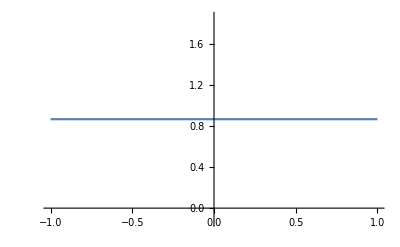

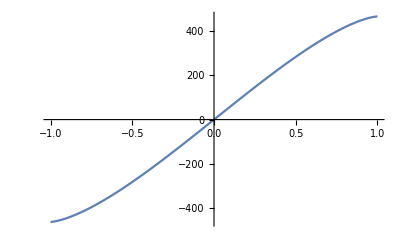

```mathematica
Plot[Re[theta[u]], {u, -1, 1}, PlotRange->All]
Plot[Im[theta[u]], {u, -1, 1}, PlotRange->All]
```

```mathematica
theta[0.5]
```

0.866025+283.096 ⅈ

```mathematica
thetasec[t_] := m*g *l *Sin[theta2[t]]/Subscript[J, 1]-((Lpsi-Cos[theta2[t]*Lphi])(Lphi -Cos[theta2[t]]*Lpsi))/(Subscript[J, 1]*Sin[theta2[t]]^3);

equations = {
theta2''[u] == thetasec[u],
theta2[0] == Sqrt[3]/2,
theta2'[0] == 0};

solution =NDSolve[equations, theta[u], {u, -1, 1}]
theta2[t_] = theta2[u] /. solution[[1]]
```

NDSolve::ndsz: At u == -0.0331921, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At u == 0.0331921, step size is effectively zero; singularity or stiff system suspected.

{{InterpolatingFunction[…][u]→InterpolatingFunction[…][u]}}

theta2[u]

```mathematica
Plot[Re[theta2[u]], {u, -1, 1}, PlotRange->All]

Plot[Im[theta2[u]], {u, -1, 1}, PlotRange->All]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

-Graphics-

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

-Graphics-